```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
m=4;
P=16;
T=1280-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[1,P];
mu⟦2⟧=RandomInteger[1,P];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,1},{j,1,3}]~Join~Table[0,{i,1,n-1},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S},{i,1,T}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=300;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[10*Price⟦1⟧,{i,1,n}];
c=Table[10*Price⟦1⟧,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
fiΔS=Table[0,{i,1,n}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s,1⟧≥Max[U⟦i,All,1⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
U⟦1,All,1⟧
```

{1,1}

```mathematica
(Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
BS⟦1,3⟧=BS⟦1,2⟧;
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s,t⟧≥Max[U⟦i,All,t⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
If[t>T/2,fiΔS⟦1⟧=fiΔS⟦1⟧+(1-KroneckerDelta[BS⟦1,3⟧,BS⟦1,1⟧])];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
If[t>T/2,Do[fiΔS⟦i⟧=fiΔS⟦i⟧+(1-KroneckerDelta[BS⟦i,2⟧,BS⟦i,1⟧]),{i,n1+1,n}]];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=10*Price⟦T⟧,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];Do[W⟦i⟧=100,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
ΔcM⟦t⟧=+A⟦t-1⟧*Price⟦t⟧;
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦1,s⟧=0,{s,1,S}];,
Do[PayoffFunction⟦1,s⟧=(AgentStrategy⟦1,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s,t+1⟧=U⟦i,s,t⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

Set::partw: Part 1280 of {1, 1, 1, 1, 4, 4, -43, -43, -42, -42, -31, -31, -40, -40, -27, -27, -20, -20, -23, -23, -22, -22, -23, -23, -4, -4, -1, -1, 10, 10, -5, -5, -32, -32, -59, -59, -60, -60, -61, -61, -58, -58, -51, -51, -50, -50, -45, -45, -44, -44, « 1229 »} does not exist.

Set::partw: Part 1280 of {1, 1, 1, -2, -5, -16, 31, 38, 39, 56, 67, 48, 39, 34, 47, 46, 53, 32, 29, 28, 27, -8, -7, -12, -31, -24, -27, 2, -9, 0, 15, -6, -33, -22, 5, -14, -15, 8, 9, 10, 7, -2, -9, -10, -11, -34, -39, -24, -23, -10, « 1229 »} does not exist.

Set::partw: Part 1280 of {1, 1, 1, -2, -5, -16, 31, 24, 25, 42, 53, 34, 25, 20, 33, 32, 25, 4, 7, 8, 7, -28, -27, -32, -51, -44, -41, -12, -1, -10, 5, -16, -43, -32, -5, -24, -25, -2, -1, 0, -3, 6, -1, -2, -3, -26, -31, -16, -15, -2, « 1229 »} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

{11.34265,Null}

```mathematica
fiΔS
```

{33,0,4,0,65,6,0,0,38,30,0,0,22,60,43,0,0,12,0,0,49,10,0,15,12,31,0,0,0,0,81,35,6,0,0,0,48,0,0,43,0,0,0,35,56,79,46,22,56,0,17,43,20,0,0,27,0,53,0,0,2,41,0,0,65,39,0,26,8,0,0,12,0,11,4,4,40,8,58,0,49,0,10,14,24,0,21,42,60,0,8,0,55,0,9,0,24,30,0,0,0}

```mathematica
Count[fiΔS,0]
```

45

```mathematica
A
N[-ΔcM,4]
N[Table[A⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,0,7,-1,-53,17,-5,-25,5}

{0,0,-74.88,10.6,282.1,-119.3,32.59,100.7,0}

{74.88,-10.6,-282.1,119.3,-32.59,-100.7}

```mathematica
nM
N[Price,4]
```

{0,0,0,-7,-6,47,30,35,60}

{10.,10.,10.,10.7,10.6,5.323,7.015,6.517,4.03}

```mathematica
N[Table[-nM⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,90.,0,-205.2,-142.4,-172.4}

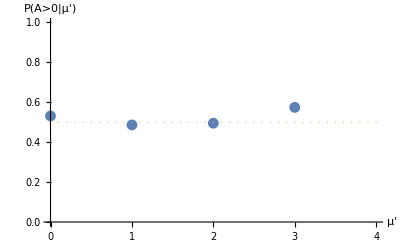

```mathematica
"P(1|μ4),P(1|μ6)";
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T/2)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[{Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Table[{i/10,0.5},{i,0,10P}]},PlotStyle->{Filling,PointSize[0.002]},PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ'","P(A>0|μ')"}]
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

```mathematica
N[Variance[A]]
```

55.9457

```mathematica
1/(n*T)Sum[(A⟦i⟧-(Mean[A]))^2,{i,1,T}]//N
```

0.553572

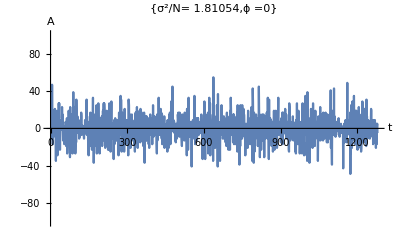

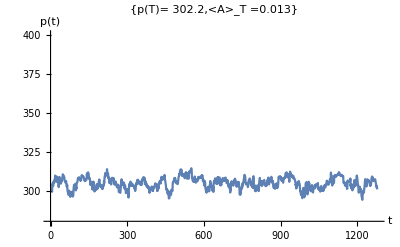

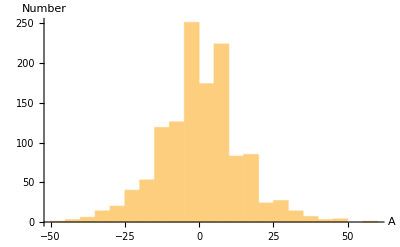

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->{"σ^2/N= "<>ToString[N[1/n Variance[A]]],"ϕ ="<>ToString[N[1/n Count[fiΔS,0],2]]}]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","p(t)"},PlotRange->{{0,T},{280,400}},Joined->True,PlotLabel->{"p(T)= "<>ToString[N[Price⟦T⟧,4]],"<A>_T ="<>ToString[N[Mean[A],2]]},LabelStyle-> {12,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

```mathematica
1/(n*T)Sum[(A⟦i⟧)^2,{i,1,n}]//N
```

0.465607

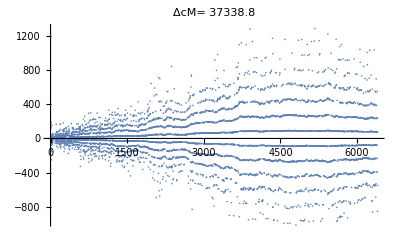

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦1;;T⟧]]]]
```

```mathematica
-Total[ΔcM⟦1;;T⟧]+(9n-nM⟦T⟧)*Price⟦T⟧-(9n*Price⟦1⟧)//N
```

```mathematica
W⟦1⟧
```

-197.516

```mathematica
W⟦2⟧
```

8532.94

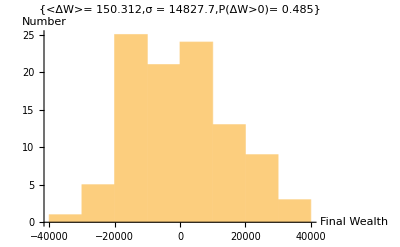

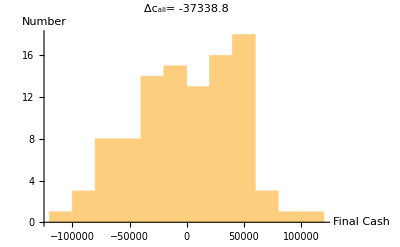

```mathematica
f4=Histogram[W⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Wealth","Number"},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-100]]],"σ = "<>ToString[N[StandardDeviation[W-100]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-100]],3]]}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
c
```

{-117.913,2742.89,-6467.88,507.166,-15793.9,-7877.01,2937.71,12886.8,16011.4,5602.37,-2623.22,13986.4,8147.35,-585.691,-15287.1,-10469.4,7017.31,11421.5,-3769.09,-1811.38,-15420.,-13.6204,-12353.,-4512.65,-15424.3,-1994.65,-12016.4,-13632.5,3716.09,10951.5,7743.28,7701.99,4525.05,4759.5,-12894.1,10824.7,-8774.24,13832.5,-12025.,22391.8,7784.61,7711.14,-1155.05,3723.66,-4565.58,5531.06,12931.2,12880.6,6209.06,-12902.7,-12179.5,65.8824,-8060.59,-6415.14,-11475.,14451.6,8774.72,-16664.1,1988.24,-7848.19,-7736.45,-5882.2,8294.03,702.29,4445.94,-12353.,-6144.4,-9079.44,-15455.4,11760.8,-7721.12,16191.8,-6664.5,-11517.2,-10866.5,22351.9,485.469,-6436.84,-6529.36,10912.,-6418.1,-3852.37,-11626.9,-5141.01,-1659.12,6960.28,4652.83,-9069.69,6844.47,14452.5,-16676.,-11381.2,-2028.88,-11958.1,507.166,-4742.42,-8723.7,-15356.6,-926.169,14451.6,14442.8}